## Brian — PS 7 — 2025-02-11 — Solution

## EIWL3 Sections 18 and 19

## Exercises from EIWL3 Section 18

```mathematica
options=GeoServer->{Automatic,"GlobalTimeout"->180,"ConnectionRetryCount"->6};
```

```mathematica
(* 18.1 *) GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]
```

3453.71 mi

```mathematica
(* 18.2 *) GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"London","GreaterLondon","UnitedKingdom"}]]/GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"SanFrancisco","California","UnitedStates"}]]
```

1.35109

```mathematica
(* 18.3 *) UnitConvert[GeoDistance[Entity["City",{"Sydney","NewSouthWales","Australia"}],Entity["City",{"Moscow","Moscow","Russia"}]],Quantity[, "Kilometers"]]
```

14387. km

```mathematica
(* 18.4 *) GeoGraphics[Entity["Country","Luxembourg"],options]
```

-Graphics-

```mathematica
(* 18.5 *) GeoListPlot[{Entity["Country","Brazil"],Entity["Country","Russia"],Entity["Country","India"],Entity["Country","China"]}]
```

-Graphics-

```mathematica
(* 18.6 *) GeoGraphics[GeoPath[{Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}]}],options]
```

-Graphics-

```mathematica
(* 18.7 *) GeoGraphics[GeoDisk[Entity["HistoricalSite","GreatPyramidOfGiza::kbgx6"],10 Quantity[, "Miles"]]]
```

-Graphics-

```mathematica
(* 18.8 *) GeoGraphics[GeoDisk[Entity["City",{"NewYork","NewYork","UnitedStates"}],GeoDistance[Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Amherst","NewYork","UnitedStates"}]]],options]
```

-Graphics-

```mathematica
(* 18.9 *) GeoImage[GeoDisk[Entity["Building","ThePentagon::qzh8d"],0.4 Quantity[, "Miles"]]]
```

-Graphics-

```mathematica
(* 18.10 *) GeoNearest["Country",GeoPosition["NorthPole"],5]
```

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* 18.11 *) EntityValue[GeoNearest["Country",GeoPosition[{45,0}],3],"Flag"]
```

```mathematica
(* 18.12 *) GeoListPlot[GeoNearest["Volcano",Entity["City",{"Rome","Lazio","Italy"}],25]]
```

-Graphics-

```mathematica
(* 18.13 *) EntityValue[Entity["City",{"NewYork","NewYork","UnitedStates"}],"Latitude"]-EntityValue[Entity["City",{"LosAngeles","California","UnitedStates"}],"Latitude"]
```

6.64488 °

## Exercises from EIWL3 Section 19

```mathematica
(* 19.1 *) Today- DateObject[{1900,1,1},"Day"]
```

45697 days

```mathematica
(* 19.2 *) DayName[DateObject[{2000,1,1},"Day"]]
```

Saturday

```mathematica
(* 19.3 *) Today-100000 Quantity[, "Days"]
```

Thu 29 Apr 1751

```mathematica
(* 19.4 *) LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

Tue 11 Feb 2025 19:47:14GMT+5.5

```mathematica
(* 19.5 *) Sunset[Entity["City",{"Bishop","California","UnitedStates"}], Today]-Sunrise[Entity["City",{"Bishop","California","UnitedStates"}], Today]
```

10.7219 h

```mathematica
(* 19.6 *) MoonPhase[Today,"Icon"]
```

-Graphics-

```mathematica
(* 19.7 *) Table[MoonPhase[Today+i Quantity[, "Days"]],{i,10}]
```

{0.998647,0.993907,0.969673,0.927894,0.870882,0.801093,0.720987,0.632977,0.539487,0.443082}

```mathematica
(* 19.8 *) Table[MoonPhase[Today+i Quantity[, "Days"],"Icon"],{i,0,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* The next one gave an annoyingly wrong answer until I *) (* forced it to do something better by changing the date *)
(* for London. Until I did that, it was *)(* getting tomorrow's sunrise in London, *)(* because tomorrow's sunrise in London occurs just *)(* before midnight in California. *)
(* Ptooey. *)

(* 19.9 *) Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],  DateObject[{2025,2,11},"Day"]]-Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}],  DateObject[{2025,2,10},"Day"]]
```

4.54772 h

```mathematica
(* 19.10 *)UnitConvert[Today-Entity["MannedSpaceMission","Apollo11"][EntityProperty["MannedSpaceMission","LunarLandingDate"]],Quantity[, "Years"]]
```

278/5 yr

```mathematica
(* 19.11 *)
yesterdayNoonInFrance=LocalTime[Entity["Country","France"],DateObject[{2025,2,10,12,0,0},"Instant","Gregorian","Europe/Berlin"]];
AirTemperatureData[ Entity["Building","EiffelTower::5h9w8"],yesterdayNoonInFrance]
```

41. °F

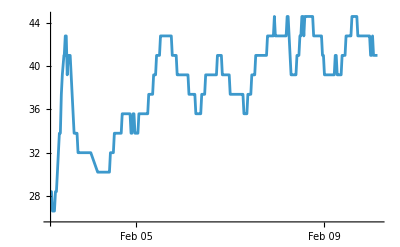

```mathematica
(* 19.12 *) ListLinePlot[AirTemperatureData[ Entity["Building","EiffelTower::5h9w8"],{yesterdayNoonInFrance-7 Quantity[, "Days"],yesterdayNoonInFrance}]]
```

```mathematica
(* 19.13 *) AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}],Now]- AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}],Now]
```

20. _Δ^◦F

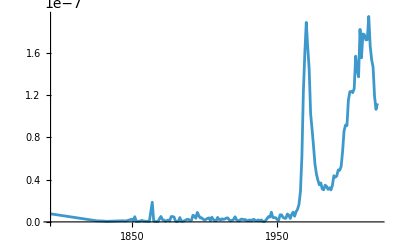

```mathematica
(* 19.14 *) ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
(* 19.15 *) Entity["Country","UnitedStates"][Dated["Population",2000]]-Entity["Country","UnitedStates"][Dated["Population",1900]]
```

2.04604×10^8 people